### Examen 2 de Variable Compleja

```mathematica
Sec[(Pi/2)-I]
```

-ⅈ Csch[1]

```mathematica
ComplexExpand[Log[-3+I]]
```

ⅈ (π-ArcTan[1/3])+Log[10]/2

```mathematica
ComplexExpand[(-I)^I]
```

ⅇ^(π/2)

```mathematica
??Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.

Attributes[Piecewise]={HoldAll,Protected,ReadProtected}
 
Piecewise/:Default[Piecewise,2]:=0

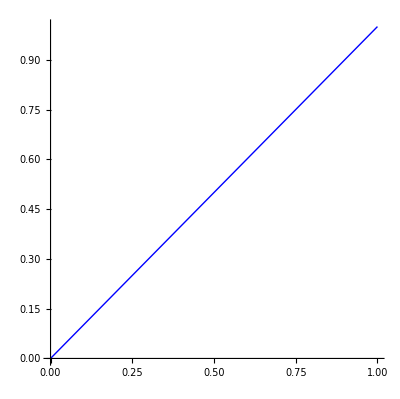

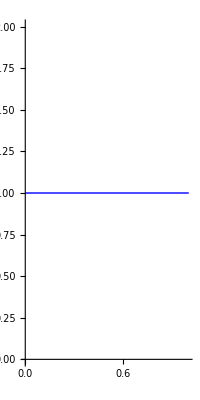

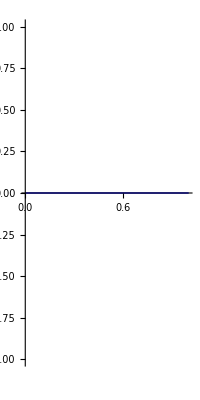

```mathematica
f1=Plot[x,{x,0,1},PlotStyle->Directive[Blue,Thickness[0.0025]],AspectRatio->Automatic]
f2=Plot[1,{x,0,1},PlotStyle->Directive[Blue,Thickness[0.0025]],AspectRatio->Automatic]
f3=Plot[0,{y,0,1},PlotStyle->Directive[Blue,Thickness[0.0025]],AspectRatio->Automatic]
```

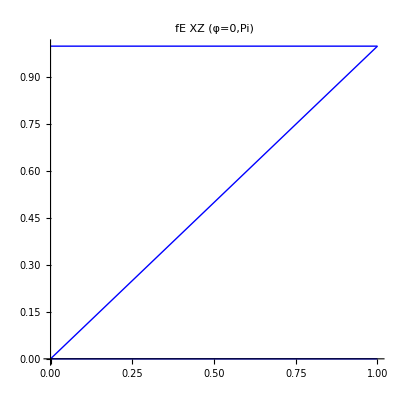

```mathematica
Show[f1,f2,f3,PlotLabel->"fE XZ (φ=0,Pi)"]
```

```mathematica
Integrate[2x-6I*x^2,{x,0,1}]+I*Integrate[2x-6I*x^2,{x,0,1}]
```

3-ⅈ

```mathematica
Piecewise[{{y,0<x<1}}]
```

Piecewise[{{y, 0<x<1}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{y,0<x<1}},0]]
```

Piecewise[{{y, 0<x<1}, {0, True}}]

```mathematica
Plot[%,{y,0,1} ]
```

-Graphics-